```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=20;
Ly=20;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianWSM[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[m*Cons-t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]
```

```mathematica
Clear[mVector]
```

```mathematica
mVector = N@Subdivide[-3,3,90]
```

{-3.,-2.93333,-2.86667,-2.8,-2.73333,-2.66667,-2.6,-2.53333,-2.46667,-2.4,-2.33333,-2.26667,-2.2,-2.13333,-2.06667,-2.,-1.93333,-1.86667,-1.8,-1.73333,-1.66667,-1.6,-1.53333,-1.46667,-1.4,-1.33333,-1.26667,-1.2,-1.13333,-1.06667,-1.,-0.933333,-0.866667,-0.8,-0.733333,-0.666667,-0.6,-0.533333,-0.466667,-0.4,-0.333333,-0.266667,-0.2,-0.133333,-0.0666667,0.,0.0666667,0.133333,0.2,0.266667,0.333333,0.4,0.466667,0.533333,0.6,0.666667,0.733333,0.8,0.866667,0.933333,1.,1.06667,1.13333,1.2,1.26667,1.33333,1.4,1.46667,1.53333,1.6,1.66667,1.73333,1.8,1.86667,1.93333,2.,2.06667,2.13333,2.2,2.26667,2.33333,2.4,2.46667,2.53333,2.6,2.66667,2.73333,2.8,2.86667,2.93333,3.}

```mathematica
mVector={-3.,-2.933333333333333,-2.8666666666666667,-2.8,-2.7333333333333334,-2.6666666666666665,-2.6,-2.533333333333333,-2.466666666666667,-2.4,-2.3333333333333335,-2.2666666666666666,-2.2,-2.1333333333333333,-2.066666666666667,-2.,-1.9333333333333333,-1.8666666666666667,-1.8,-1.7333333333333334,-1.6666666666666667,-1.6,-1.5333333333333334,-1.4666666666666666,-1.4,-1.3333333333333333,-1.2666666666666666,-1.2,-1.1333333333333333,-1.0666666666666667,-1.,-0.9333333333333333,-0.8666666666666667,-0.8,-0.7333333333333333,-0.6666666666666666,-0.6,-0.5333333333333333,-0.4666666666666667,-0.4,-0.3333333333333333,-0.26666666666666666,-0.2,-0.13333333333333333,-0.06666666666666667,0.06666666666666667,0.13333333333333333,0.2,0.26666666666666666,0.3333333333333333,0.4,0.4666666666666667,0.5333333333333333,0.6,0.6666666666666666,0.7333333333333333,0.8,0.8666666666666667,0.9333333333333333,1.,1.0666666666666667,1.1333333333333333,1.2,1.2666666666666666,1.3333333333333333,1.4,1.4666666666666666,1.5333333333333334,1.6,1.6666666666666667,1.7333333333333334,1.8,1.8666666666666667,1.9333333333333333,2.,2.066666666666667,2.1333333333333333,2.2,2.2666666666666666,2.3333333333333335,2.4,2.466666666666667,2.533333333333333,2.6,2.6666666666666665,2.7333333333333334,2.8,2.8666666666666667,2.933333333333333,3.}
```

{-3.,-2.93333,-2.86667,-2.8,-2.73333,-2.66667,-2.6,-2.53333,-2.46667,-2.4,-2.33333,-2.26667,-2.2,-2.13333,-2.06667,-2.,-1.93333,-1.86667,-1.8,-1.73333,-1.66667,-1.6,-1.53333,-1.46667,-1.4,-1.33333,-1.26667,-1.2,-1.13333,-1.06667,-1.,-0.933333,-0.866667,-0.8,-0.733333,-0.666667,-0.6,-0.533333,-0.466667,-0.4,-0.333333,-0.266667,-0.2,-0.133333,-0.0666667,0.0666667,0.133333,0.2,0.266667,0.333333,0.4,0.466667,0.533333,0.6,0.666667,0.733333,0.8,0.866667,0.933333,1.,1.06667,1.13333,1.2,1.26667,1.33333,1.4,1.46667,1.53333,1.6,1.66667,1.73333,1.8,1.86667,1.93333,2.,2.06667,2.13333,2.2,2.26667,2.33333,2.4,2.46667,2.53333,2.6,2.66667,2.73333,2.8,2.86667,2.93333,3.}

```mathematica
aaaaa=Dimensions[mVector][[1]]
```

90

```mathematica
(**OBC**)
```

```mathematica
(* Clear[b];
b={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM[1.,1.,4,1,kzVector[[i]],0]],
Do[b=Append[b,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,aaaaa}] *)
```

```mathematica
(* ListPlot[b] *)
```

```mathematica
(**PBC**)
```

```mathematica
(*Clear[bb];
bb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM[1.,1.,4,1,kzVector[[i]],1]],
Do[bb=Append[bb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,aaaaa}]*)
```

```mathematica
(*ListPlot[bb]*)
```

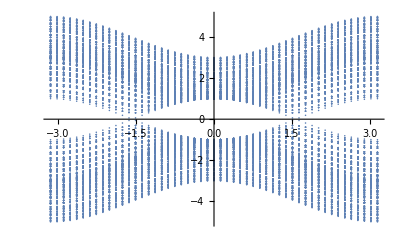

-Graphics-

```mathematica
(**----Clear memory for quasicrystal----**)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

800

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=(2/(3))*(x-1)+8
LineDn[x_]:=(2/(3))*(x-2)+6
```

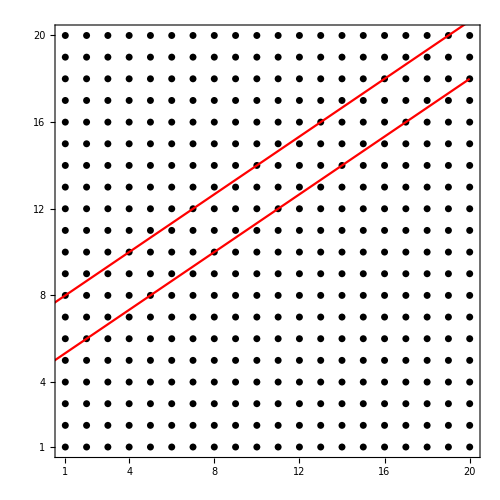

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, Ux, Vy, P,U,V,LogEigenValuesBott,Bott, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{101,121,122,123,142,143,144,163,164,165,166,185,186,187,206,207,208,209,228,229,230,249,250,251,252,271,272,273,292,293,294,295,314,315,316,335,336,337,338,357,358,359,378,379,380,400}

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{201,202,241,242,243,244,245,246,283,284,285,286,287,288,325,326,327,328,329,330,331,332,369,370,371,372,373,374,411,412,413,414,415,416,417,418,455,456,457,458,459,460,497,498,499,500,501,502,503,504,541,542,543,544,545,546,583,584,585,586,587,588,589,590,627,628,629,630,631,632,669,670,671,672,673,674,675,676,713,714,715,716,717,718,755,756,757,758,759,760,799,800}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

92

```mathematica
NOrbitalsQuasi/2
```

46

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

708

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.115

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{800}

```mathematica
(**-- a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
] --**)
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(**-------------------------------**)
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi/2-1}]
```

{{1.,0},{1.9245,0},{2.4792,0},{3.4037,0},{4.3282,0},{4.8829,0},{5.8074,0},{6.7319,0},{7.2866,0},{8.2111,0},{9.1356,0},{9.6903,0},{10.6148,0},{11.5393,0},{12.094,0},{13.0185,0},{13.943,0},{14.4977,0},{15.4222,0},{16.3467,0},{16.9014,0},{17.8259,0},{18.7504,0},{19.3051,0},{20.2296,0},{21.1541,0},{21.7088,0},{22.6333,0},{23.5578,0},{24.1125,0},{25.037,0},{25.9615,0},{26.5162,0},{27.4407,0},{28.3652,0},{28.9199,0},{29.8444,0},{30.7689,0},{31.3236,0},{32.2481,0},{33.1726,0},{33.7273,0},{34.6518,0},{35.5763,0},{36.131,0},{37.0555,0}}

```mathematica
Clear[xx,yy]
```

```mathematica
xx={};
yy={};
```

```mathematica
Do[{s=Solve[y==LineDn[x]&& (y-YList[[k]])/(x-XList[[k]])==-((1+√5)/2) ,{x,y}],xx = Append[xx,s[[All,1,2]]],yy = Append[yy,s[[All,2,2]]]},{k,1,NOrbitalsQuasi/2}]
```

```mathematica
N[xx]
```

{{1.2918},{1.72949},{2.43769},{3.1459},{2.87539},{3.58359},{4.2918},{4.02129},{4.72949},{5.43769},{6.1459},{5.87539},{6.58359},{7.2918},{7.02129},{7.72949},{8.43769},{9.1459},{8.87539},{9.58359},{10.2918},{10.0213},{10.7295},{11.4377},{12.1459},{11.8754},{12.5836},{13.2918},{13.0213},{13.7295},{14.4377},{15.1459},{14.8754},{15.5836},{16.2918},{16.0213},{16.7295},{17.4377},{18.1459},{17.8754},{18.5836},{19.2918},{19.0213},{19.7295},{20.4377},{20.8754}}

```mathematica
N[yy]
```

{{5.52786},{5.81966},{6.2918},{6.76393},{6.58359},{7.05573},{7.52786},{7.34752},{7.81966},{8.2918},{8.76393},{8.58359},{9.05573},{9.52786},{9.34752},{9.81966},{10.2918},{10.7639},{10.5836},{11.0557},{11.5279},{11.3475},{11.8197},{12.2918},{12.7639},{12.5836},{13.0557},{13.5279},{13.3475},{13.8197},{14.2918},{14.7639},{14.5836},{15.0557},{15.5279},{15.3475},{15.8197},{16.2918},{16.7639},{16.5836},{17.0557},{17.5279},{17.3475},{17.8197},{18.2918},{18.5836}}

```mathematica
N[Sqrt[xx^2+yy^2]]
```

{{5.6768},{6.07121},{6.74752},{7.45972},{7.18412},{7.91362},{8.66535},{8.37597},{9.13866},{9.91577},{10.7041},{10.4018},{11.196},{11.9979},{11.6908},{12.4968},{13.3085},{14.1248},{13.8125},{14.6313},{15.4536},{15.1391},{15.9633},{16.7901},{17.6193},{17.3024},{18.1328},{18.9651},{18.647},{19.4803},{20.3151},{21.1512},{20.8317},{21.6685},{22.5064},{22.1862},{23.0247},{23.8641},{24.7043},{24.3833},{25.224},{26.0653},{25.7439},{26.5856},{27.4279},{27.9487}}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

38

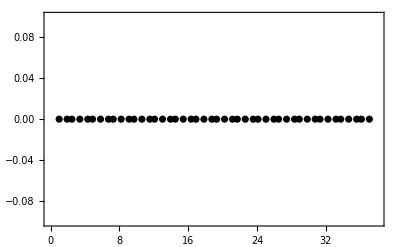

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black]
```

```mathematica
Fibon1D[[3,1]]
```

2.4792

```mathematica
(**-------------------------------**)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[TabFibNew]
```

```mathematica
TabFibNew={}
```

{}

```mathematica
Do[{Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D],
HTrial=HamiltonianWSM[1.,1.,mVector[[p]],1],
(*---------------------------------------------------------*)
Hfbfb[i_Integer,j_Integer]=0,
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
],
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}],
(*---------------------------------------------------------*)
H2d2d[i_Integer,j_Integer]=0,
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
],
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}],
(*------------------------------------------------------*)
H2dfb[i_Integer,j_Integer]=0,

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
],
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}],
(*-------------------------------------------------*)
Hfb2d[i_Integer,j_Integer]=0,

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
],
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}],

(*---------------------------------------------------------------------------------------------------------------------------------*)
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon],
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB),
(**------Check that HFibonRenor is Hermitian------**)
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
ValueFibon=Sort[Re[Eigenvalues[HFibonRenor]]],
TabFibNew = Append[TabFibNew,{mVector[[p]],ValueFibon[[(NOrbitalsQuasi/2 )+ 1]]-ValueFibon[[NOrbitalsQuasi/2]]}]
},{p,1,aaaaa}]
```

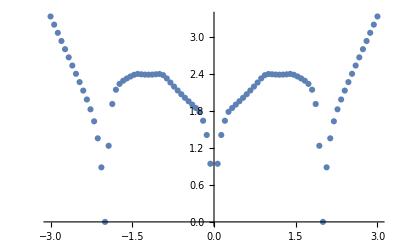

```mathematica
ListPlot[TabFibNew,PlotRange->All]
```

```mathematica
TabFibNew
```

{{-3.,3.33155},{-2.93333,3.19881},{-2.86667,3.06614},{-2.8,2.93352},{-2.73333,2.80093},{-2.66667,2.66828},{-2.6,2.53542},{-2.53333,2.40198},{-2.46667,2.2672},{-2.4,2.12945},{-2.33333,1.98507},{-2.26667,1.82566},{-2.2,1.6315},{-2.13333,1.35525},{-2.06667,0.884569},{-2.,3.88646×10^-15},{-1.93333,1.23429},{-1.86667,1.91194},{-1.8,2.14343},{-1.73333,2.238},{-1.66667,2.28899},{-1.6,2.3262},{-1.53333,2.35818},{-1.46667,2.38555},{-1.4,2.39982},{-1.33333,2.3932},{-1.26667,2.38867},{-1.2,2.38747},{-1.13333,2.38941},{-1.06667,2.39396},{-1.,2.39829},{-0.933333,2.37972},{-0.866667,2.32665},{-0.8,2.25986},{-0.733333,2.19439},{-0.666667,2.13114},{-0.6,2.07042},{-0.533333,2.01225},{-0.466667,1.95639},{-0.4,1.90207},{-0.333333,1.84718},{-0.266667,1.78511},{-0.2,1.64043},{-0.133333,1.40935},{-0.0666667,0.94298},{0.0666667,0.94298},{0.133333,1.40935},{0.2,1.64043},{0.266667,1.78511},{0.333333,1.84718},{0.4,1.90207},{0.466667,1.95639},{0.533333,2.01225},{0.6,2.07042},{0.666667,2.13114},{0.733333,2.19439},{0.8,2.25986},{0.866667,2.32665},{0.933333,2.37972},{1.,2.39829},{1.06667,2.39396},{1.13333,2.38941},{1.2,2.38747},{1.26667,2.38867},{1.33333,2.3932},{1.4,2.39982},{1.46667,2.38555},{1.53333,2.35818},{1.6,2.3262},{1.66667,2.28899},{1.73333,2.238},{1.8,2.14343},{1.86667,1.91194},{1.93333,1.23429},{2.,3.88646×10^-15},{2.06667,0.884569},{2.13333,1.35525},{2.2,1.6315},{2.26667,1.82566},{2.33333,1.98507},{2.4,2.12945},{2.46667,2.2672},{2.53333,2.40198},{2.6,2.53542},{2.66667,2.66828},{2.73333,2.80093},{2.8,2.93352},{2.86667,3.06614},{2.93333,3.19881},{3.,3.33155}}

```mathematica
IrrationalData= {{-3.,3.151707387793979},{-2.933333333333333,3.0204614841408404},{-2.8666666666666667,2.8893893087931195},{-2.8,2.7584938235451584},{-2.7333333333333334,2.627761179392466},{-2.6666666666666665,2.497141608866065},{-2.6,2.366509834733459},{-2.533333333333333,2.2355809256651495},{-2.466666666666667,2.1037257126573476},{-2.4,1.9695510950808521},{-2.3333333333333335,1.8299097346600175},{-2.2666666666666666,1.6774836087243585},{-2.2,1.4947472499040115},{-2.1333333333333333,1.2388408068434114},{-2.066666666666667,0.8064356443053302},{-2.,3.1918146944466855*^-15},{-1.9333333333333333,1.0814024651017005},{-1.8666666666666667,1.6567137207986442},{-1.8,1.858229038874688},{-1.7333333333333334,1.9473194468992414},{-1.6666666666666667,2.0027384639576833},{-1.6,2.04773301620449},{-1.5333333333333334,2.08936861477571},{-1.4666666666666666,2.129622323463795},{-1.4,2.168131726035647},{-1.3333333333333333,2.203324157791714},{-1.2666666666666666,2.234196732909757},{-1.2,2.2578358928540543},{-1.1333333333333333,2.2759514297592713},{-1.0666666666666667,2.276586345827181},{-1.,2.2674481558006043},{-0.9333333333333333,2.2516138537469477},{-0.8666666666666667,2.2169276857558344},{-0.8,2.1710831609612953},{-0.7333333333333333,2.111184930671997},{-0.6666666666666666,2.049508825360059},{-0.6,1.9882873428685084},{-0.5333333333333333,1.928091311956679},{-0.4666666666666667,1.8689132592275137},{-0.4,1.8100937131749797},{-0.3333333333333333,1.7481955946247627},{-0.26666666666666666,1.6372544055283484},{-0.2,1.4950936594480264},{-0.13333333333333333,1.275936812348939},{-0.06666666666666667,0.8479725951831655},{0.06666666666666667,0.8479725951831655},{0.13333333333333333,1.275936812348939},{0.2,1.4950936594480264},{0.26666666666666666,1.6372544055283484},{0.3333333333333333,1.7481955946247627},{0.4,1.8100937131749797},{0.4666666666666667,1.8689132592275137},{0.5333333333333333,1.928091311956679},{0.6,1.9882873428685084},{0.6666666666666666,2.049508825360059},{0.7333333333333333,2.111184930671997},{0.8,2.1710831609612953},{0.8666666666666667,2.2169276857558344},{0.9333333333333333,2.2516138537469477},{1.,2.2674481558006043},{1.0666666666666667,2.276586345827181},{1.1333333333333333,2.2759514297592713},{1.2,2.2578358928540543},{1.2666666666666666,2.234196732909757},{1.3333333333333333,2.203324157791714},{1.4,2.168131726035647},{1.4666666666666666,2.129622323463795},{1.5333333333333334,2.08936861477571},{1.6,2.04773301620449},{1.6666666666666667,2.0027384639576833},{1.7333333333333334,1.9473194468992414},{1.8,1.858229038874688},{1.8666666666666667,1.6567137207986442},{1.9333333333333333,1.0814024651017027},{2.,3.1918146944466855*^-15},{2.066666666666667,0.8064356443053302},{2.1333333333333333,1.2388408068434114},{2.2,1.4947472499040115},{2.2666666666666666,1.6774836087243585},{2.3333333333333335,1.8299097346600175},{2.4,1.9695510950808521},{2.466666666666667,2.1037257126573476},{2.533333333333333,2.2355809256651495},{2.6,2.3665098347334625},{2.6666666666666665,2.497141608866065},{2.7333333333333334,2.627761179392466},{2.8,2.7584938235451584},{2.8666666666666667,2.8893893087931195},{2.933333333333333,3.0204614841408404},{3.,3.151707387793979}};
```

```mathematica
RationalData={{-3.,3.331546029854902},{-2.933333333333333,3.198807339595268},{-2.8666666666666667,3.0661354534203227},{-2.8,2.9335194632862356},{-2.7333333333333334,2.8009270037027134},{-2.6666666666666665,2.6682817148514975},{-2.6,2.5354168354461013},{-2.533333333333333,2.40197706369264},{-2.466666666666667,2.2672044060913605},{-2.4,2.12945468644119},{-2.3333333333333335,1.9850688171627051},{-2.2666666666666666,1.8256625141353582},{-2.2,1.6315000795657633},{-2.1333333333333333,1.3552539976106754},{-2.066666666666667,0.8845687263456943},{-2.,3.8864588636232885*^-15},{-1.9333333333333333,1.2342912381548763},{-1.8666666666666667,1.9119414918753286},{-1.8,2.143427187391625},{-1.7333333333333334,2.2379986486689436},{-1.6666666666666667,2.2889886215890862},{-1.6,2.326203504568692},{-1.5333333333333334,2.358182958574403},{-1.4666666666666666,2.3855531330598305},{-1.4,2.399823319581067},{-1.3333333333333333,2.3932043751912584},{-1.2666666666666666,2.388673606491645},{-1.2,2.387470252263428},{-1.1333333333333333,2.3894146671950267},{-1.0666666666666667,2.3939614656101},{-1.,2.398292825855184},{-0.9333333333333333,2.379715871029873},{-0.8666666666666667,2.326652470792662},{-0.8,2.259859500056136},{-0.7333333333333333,2.194388704558289},{-0.6666666666666666,2.131144036646033},{-0.6,2.070417939188288},{-0.5333333333333333,2.0122461028167122},{-0.4666666666666667,1.9563871404233713},{-0.4,1.9020693547589405},{-0.3333333333333333,1.8471806259576633},{-0.26666666666666666,1.7851149897032097},{-0.2,1.6404345373913762},{-0.13333333333333333,1.4093511624602049},{-0.06666666666666667,0.9429795988602552},{0.06666666666666667,0.9429795988602552},{0.13333333333333333,1.4093511624602049},{0.2,1.6404345373913762},{0.26666666666666666,1.7851149897032097},{0.3333333333333333,1.8471806259576633},{0.4,1.9020693547589405},{0.4666666666666667,1.9563871404233713},{0.5333333333333333,2.0122461028167122},{0.6,2.070417939188288},{0.6666666666666666,2.131144036646033},{0.7333333333333333,2.194388704558289},{0.8,2.259859500056136},{0.8666666666666667,2.326652470792662},{0.9333333333333333,2.379715871029873},{1.,2.398292825855184},{1.0666666666666667,2.3939614656101},{1.1333333333333333,2.3894146671950267},{1.2,2.387470252263428},{1.2666666666666666,2.388673606491645},{1.3333333333333333,2.3932043751912584},{1.4,2.399823319581067},{1.4666666666666666,2.3855531330598305},{1.5333333333333334,2.358182958574403},{1.6,2.326203504568692},{1.6666666666666667,2.2889886215890862},{1.7333333333333334,2.2379986486689436},{1.8,2.143427187391625},{1.8666666666666667,1.9119414918753286},{1.9333333333333333,1.2342912381548763},{2.,3.8864588636232885*^-15},{2.066666666666667,0.8845687263456904},{2.1333333333333333,1.3552539976106754},{2.2,1.6315000795657641},{2.2666666666666666,1.8256625141353582},{2.3333333333333335,1.9850688171626933},{2.4,2.12945468644119},{2.466666666666667,2.2672044060913605},{2.533333333333333,2.40197706369264},{2.6,2.5354168354461013},{2.6666666666666665,2.6682817148514975},{2.7333333333333334,2.8009270037027134},{2.8,2.9335194632862356},{2.8666666666666667,3.0661354534203227},{2.933333333333333,3.198807339595268},{3.,3.331546029854902}};
```

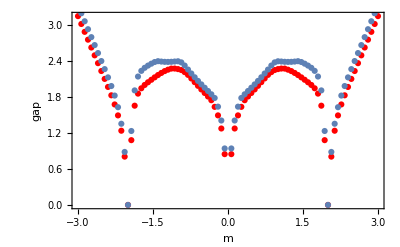

```mathematica
Show[ListPlot[IrrationalData,PlotRange->All,PlotStyle->Red],ListPlot[RationalData,PlotRange->All],Frame-> True, FrameLabel->{"m","gap"},BaseStyle->18,RotateLabel-> False,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```